```mathematica
Manipulate[
Module[{p1,p2,cx,cy,CL,fontsize},
(*Constant*)
cx=-0.2; (*Center x*)
cy=-1; (*Center y*)

CL=1;

p1 = Graphics[{FaceForm[],EdgeForm[{Thick,Black}],Rectangle[{cx-3,cy+2},{cx+3,cy+4.5}],FaceForm[GrayLevel[0.7]],EdgeForm[{Thick,Black}],Rectangle[{cx-3,cy+3},{cx+3,cy+3.5}]},
Epilog->{
Text[Style["feed",17],{cx-8.7,cy+2.5}],
Text[Style["retentate",17],{cx+9.2,cy+2.5}],
Text[Style["permeate",17],{cx-1.3,cy+6.75}],
Text[Style["membrane",17],{cx,cy+3.27}],

Arrowheads@0.02,
Arrow[{{cx-8,cy+2.5},{cx-3,cy+2.5}}],
Arrow[{{cx+3,cy+2.5},{cx+8,cy+2.5}}],
Arrow[{{cx-2,cy+4.5},{cx-2,cy+6.5}}]
},
PlotRange->{{-10,10},{-6,6}},Axes->False];

p2=Plot[(CL-C0)/L*z+C0,{z,0,L},PlotStyle->{Thick,Black},PlotRange->{{-7,16},{-1,6}},Frame->True,FrameLabel->{"distance","concentration"},LabelStyle->{17,Black},Axes->False];


Show[Switch[tap,1,p1,2,p2],ImageSize->{600,400}]
],
Grid[{
{Control[{{tap,2,""},{1->" schematic ",2->" plot "},Setter}],
Control[{{d,10,"diffusion"},5,50,5,Appearance-> "Labeled",ImageSize->Small}]},
{Control[{{C0,5,"feed"},5,85,20,Appearance-> "Labeled",ImageSize->Small}],
Control[{{L,5,"thickness"},1,15,1,Appearance-> "Labeled",ImageSize->Small}]}
},Alignment->Left]
]
```

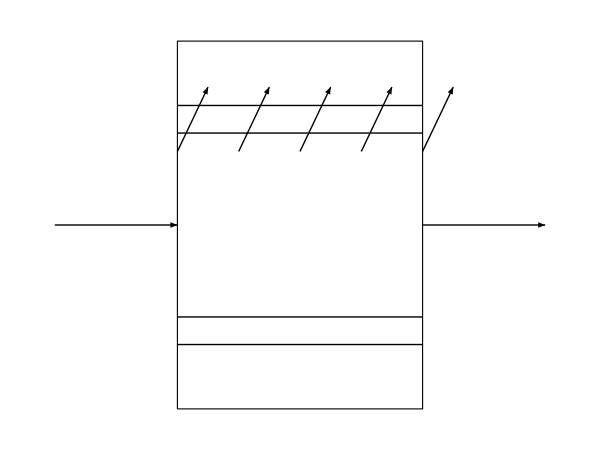

```mathematica
Module[{x0,y0,x1,y1},
x0=2;y0=1;x1=1;y1=y0/2;

Graphics[{
{EdgeForm@Thick,FaceForm@None,Rectangle[{0,0},{x0,y0}]},
{Thick,Arrow[{{-x1,y1},{0,y1}}],Arrow[{{x0,y1},{x0+x1,y1}}],
Line[{{0,#*y1},{x0,#*y1}}]&/@{0.35,0.5,1.5,1.65}},
Arrow[{{#,1.4*y1},{#+0.25,1.75*y1}}]&/@Range[0,x0,0.5]
},ImageSize->{600,450}]
]
```

```mathematica
Manipulate[
Module[{xA1,xA2,P,T,R,L,A,c,nA},
xA1=0.8;xA2=0.25;
P=1;(*atm*)T=298;(*K*)R=82.06;(*cm3 atm/mol/K*)
L=15;(*cm*)
A=π*(d/2)^2;
c=P/(R*T);(*mol/cm3*)
nA[z_]:=A*(c*χ)/z*(xA1-xA2);
Plot[nA[z],{z,0,L},PlotStyle->{Thick,Black},PlotLabel->nA[L]]
],
Control[{{d,0.1,"diameter (cm)"},0.05,0.5,0.05,Appearance->"Labeled"}],
Control[{{χ,0.784,Row@{"diffusion coefficient ",Superscript["cm",2],"/s"}},0.5,0.8,0.001,Appearance->"Labeled"}]
]
```

```mathematica
Manipulate[
Module[{d},
d=2*L;

Graphics[{
{EdgeForm@Thick,FaceForm@None,Rectangle[{0,0},{L,d}]},
{Thick,Line[{{0,#},{L,#+L}}]&/@Range[-L,d,L/10]},
{Thick,Arrowheads@0.07,
Arrow[{{-L/4,L/16},{-L/8,L/16},{L/8,L/8}}],
Arrow[{{-L/2,d/2},{-L/16,d/2}}],
Arrowheads@{-0.07,0.07},
Arrow[{{0,0.95*d},{L,0.95*d}}]},
Text[Framed[Style["L",18,Italic],Background->White,FrameStyle->None,FrameMargins->Small,RoundingRadius->10],{L/2,0.95*d}],
(*Text[Style["χ",18,Italic],{-L/4,L/16},{1,0}],*)
Text[Style[Subscript[Style["D",Italic],"AB"],18],{-L/4,L/16},{1,0}],
Text[Style[Subscript[Style["N",Italic],"A"],18],{(-L/2-L/16)/2,d/2},{0,-1}]
},ImageSize->{600,450},PlotRange->{0,d}]
],
Control[{{L,1,"diameter (cm)"},0.5,5,0.5,Appearance->"Labeled"}]
]
```

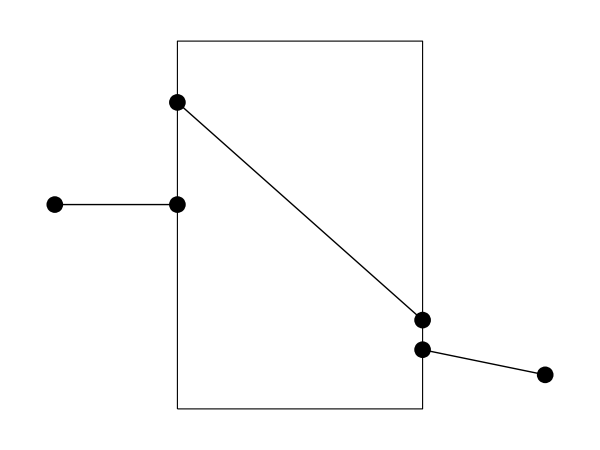

```mathematica
Module[{C1,C2,L,k,kc1,kc2,χ,Π,nA,C1i,C2i,C1is,C2is,d},
C1=0.03;C2=0.005;(*kmol/m3*)
L=3*^-5;(*m*)
k=1.5;kc1=100;kc2=2.02*^-5;(*m/s*)
χ=7*^-11;(*m2/s*)

Π=(χ*k)/L;
nA=(C1-C2)/(1/kc1+1/Π+1/kc2);

C1i=C1-nA/kc1;
C2i=C2+nA/kc2;
C1is=k*C1i;
C2is=k*C2i;

d=1*^3*L;
Graphics[{
{EdgeForm@Thick,FaceForm@None,Rectangle[{0,0},{d,1.2*Max@{C1i,C2i,C1is,C2is}}]},
{Thick,Line[{{-0.5*d,C1},{0,C1i}}],Line[{{d,C2i},{1.5*d,C2}}],Line[{{0,C1is},{d,C2is}}]},
{PointSize@0.02,Point@{-0.5*d,C1},Point@{0,C1i},Point@{d,C2i},Point@{1.5*d,C2},Point@{0,C1is},Point@{d,C2is}}
},ImageSize->{600,450}]
]
```